# Dataset builder

## Get data from an index

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];
```

```mathematica
CreateDatabaseFromData[rawData_,name_,sector_]:=Block[{datedPrices,dates,prices,returns,datedreturns,database},
datedPrices = MapAt[QuantityMagnitude,Normal[rawData],{All,2}];
dates = datedPrices[[All,1]];
prices = datedPrices[[All,2]];
returns = Returns[prices];
datedreturns = Transpose[{Drop[dates,-1],returns}];

database = <|
		"Name"->name , "Symbol"->name, "Sector"->sector,"FirstDate"->First[dates], "LastDate"->Last[dates],
		"Dates"->dates, "Prices"->prices, "Returns"->Returns[prices],
		"DatedPrices"->Transpose[{dates,prices}], "DatedReturns"->datedreturns
	|>;
Return[database];
];

DatabaseOk[database_]:=(Head[database]=!=Missing) && (database=!=$Failed);
CreateDatabaseFromTickets[tickets_]:=Block[{database,sectors,processedDatabase,goodToGo,arguments,failed},
database = ProgressMap[FinancialData[#,"RawClose",All]&,tickets,"Label"->"Downloading stock prices"];
sectors = ProgressMap[FinancialData[#,"Sector"]&,tickets,"Label"->"Downloading stock info"];
arguments = Transpose[{database,tickets,sectors}];
goodToGo = Select[arguments,DatabaseOk[First[#]]&];
failed = Select[arguments,!DatabaseOk[First[#]]&];
processedDatabase = MapThread[CreateDatabaseFromData,Transpose[goodToGo]];
Return[{processedDatabase,failed}];
];
CreateIndexDatabase[name_]:=CreateDatabaseFromTickets[FinancialData[name,"Members"]];
CreateIndexDatabase[name_,n_]:=CreateDatabaseFromTickets[Take[FinancialData[name,"Members"],n]];
CreateIndexDatabaseSafe[name_]:=Block[{processedDatabase1,processedDatabase2,failed,newDatabase},
{processedDatabase1,failed}  = CreateIndexDatabase["SP500"];
{processedDatabase2,failed} = CreateDatabaseFromTickets[failed[[All,2]]];
newDatabase = Join[processedDatabase1,processedDatabase2];
Return[{newDatabase,failed}];
];
```

### Download and create database:

```mathematica
database = CreateIndexDatabaseSafe["SP500"];
```

```mathematica
failed[[All,2]]
```

{NYSE:LNT,NYSE:PFG,NYSE:UAL,NYSE:XEL}

```mathematica
First[database]//Length
```

500

```mathematica
Last[database]
```

{{Missing[NotAvailable],NYSE:LNT,Missing[NotAvailable]},{Missing[NotAvailable],NYSE:PFG,Missing[NotAvailable]},{Missing[NotAvailable],NASDAQ:TTWO,ElectronicGamingAndMultimedia},{Missing[NotAvailable],NYSE:UAL,Missing[NotAvailable]},{Missing[NotAvailable],NYSE:XEL,Missing[NotAvailable]}}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sp500v3.wdx"}],First[database]]
```

/home/carlos/Documentos/Programacion/EconomicComputations/Database/sp500v3.wdx

### Fix each error

```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"sp500v3.wdx"}]];
```

```mathematica
takeTwo = CreateDatabaseFromTickets[{"NASDAQ:TTWO"}];
```

```mathematica
takeTwo[[1,1]]
```

<|Name→NASDAQ:TTWO,8,DatedReturns→{{Tue 15 Apr 1997 00:00:00GMT-5.,-0.0559587},{Wed 16 Apr 1997 00:00:00GMT-5.,0.0336017},5621,{Fri 16 Aug 2019 00:00:00GMT-5.,0.0206963},{Mon 19 Aug 2019 00:00:00GMT-5.,0.0120174}}|>
 |  |  |  |

Manual process

```mathematica
CreateDatabaseFromYahooFile[name_,sector_,data_]:=Block[{dates,prices,database},
dates = Map[DateObject,Drop[data[[All,1]],1]];
prices = Drop[data[[All,5]],1];

database = <|
		"Name"->name , "Symbol"->name, "Sector"->sector,"FirstDate"->First[dates], "LastDate"->Last[dates],
		"Dates"->dates, "Prices"->prices, "Returns"->Returns[prices],
		"DatedPrices"->Transpose[{dates,prices}], "DatedReturns"->Transpose[{Drop[dates,-1],Returns[prices]}]
	|>;
Return[database];
];
```

```mathematica
FileNames["*",FileNameJoin[{NotebookDirectory[],"RawData"}]]
```

{/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/LNT.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/PFG.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/UAL.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/XEL.csv}

```mathematica
lnt = CreateDatabaseFromYahooFile[
"NYSE:LNT",
"Utilities-RegulatedElectric",
Import[
"/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/LNT.csv"
]
];
pfg = CreateDatabaseFromYahooFile[
"NYSE:PFG",
"Insurance-Life",
Import[
"/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/PFG.csv"
]
];
ual = CreateDatabaseFromYahooFile[
"NYSE:UAL",
"Airlines",
Import[
"/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/UAL.csv"
]
];
xel = CreateDatabaseFromYahooFile[
"NYSE:XEL",
"Utilities-RegulatedElectric",
Import[
"/home/carlos/Documentos/Programacion/EconomicComputations/Database/RawData/XEL.csv"
]
];
```

### Assemble

```mathematica
assembled = Join[database,{takeTwo[[1,1]],lnt,pfg,ual,xel}];
```

```mathematica
Length[assembled]
```

505

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sp500v4.wdx"}],assembled]
```

/home/carlos/Documentos/Programacion/EconomicComputations/Database/sp500v4.wdx

```mathematica
database = assembled;
```

## Fix sectors

```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"sp500vULTIMATE.wdx"}]];
```

```mathematica
badSector = Position[database[[All,"Sector"]],_?(Head[#]===Missing&)]
```

{{94},{137},{163},{338},{351},{367},{395},{448}}

Fix missing sectors

```mathematica
missingSector = Extract[database,badSector][[All,"Symbol"]]
```

{NASDAQ:CBOE,NYSE:CSX,NYSE:DD,NYSE:NWL,NASDAQ:NCLH,NYSE:PEP,NYSE:REG,NYSE:UA-C}

```mathematica
FixKeyInMarket[market_,keyName_,newValue_]:=Replace[market,<|x___,keyName->_,y___|>:><|x,keyName->newValue,y|>];
FixMarket[database_,marketName_,keyName_,newValue_]:=FixKeyInMarket[First[Select[database,#["Name"]==marketName&]],keyName,newValue];
```

```mathematica
cboe = FixMarket[database,"NASDAQ:CBOE","Sector","FinancialExchanges"];
csx = FixMarket[database,"NYSE:CSX","Sector","Railroads"];
dd = FixMarket[database,"NYSE:DD","Sector","Chemicals"];
nwl = FixMarket[database,"NYSE:NWL","Sector","HouseholdAndPersonalProducts"];
nclh = FixMarket[database,"NASDAQ:NCLH","Sector","Leisure"];
pep = FixMarket[database,"NYSE:PEP","Sector","Beverages-SoftDrinks"];
reg = FixMarket[database,"NYSE:REG","Sector","REIT-Retail"];
uac = FixMarket[database,"NYSE:UA-C","Sector","ApparelManufacturing"];
```

```mathematica
tempDatabase = Delete[database,badSector];
```

```mathematica
joined = Join[tempDatabase,{cboe,csx,dd,nwl,nclh,pep,reg,uac}];
```

```mathematica
sorted = SortBy[joined,#["Name"]&];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sp500vULTIMATE.wdx"}],sorted]
```

/home/carlos/Documentos/Programacion/EconomicComputations/Database/sp500vULTIMATE.wdx

```mathematica
database = sorted;
```

```mathematica
sorted[[All,"Name"]]
```

## Fix dates

```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"sp500v1.wdx"}]];
databaseSizes = SortBy[Map[MapAt[Length,#,Key["Prices"]]&,database[[All,{"Name","Prices"}]]],#["Prices"]&];
```

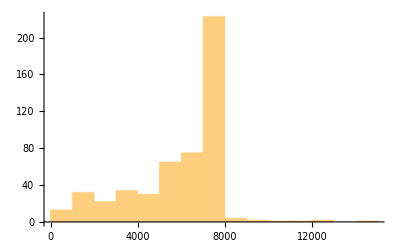

```mathematica
Histogram[databaseSizes[[All,"Prices"]]]
```

```mathematica
N[(Length@Select[databaseSizes,#["Prices"]<4000&])/505]
```

0.2

```mathematica
recentStock = Select[databaseSizes,#["Prices"]<4000&][[All,"Name"]];
withoutRecent = Select[database,!MemberQ[recentStock,#["Name"]]&];
minDate = Max@withoutRecent[[All,"FirstDate"]];
maxDate = Min@withoutRecent[[All,"LastDate"]];
interval = {DateObject[minDate,"Day"],DateObject[maxDate,"Day"]}
```

{Day: Fri 31 Jan 2003,Day: Tue 13 Nov 2018}

```mathematica
First[database] // Keys
```

{Name,Symbol,Sector,FirstDate,LastDate,Dates,Prices,Returns,DatedPrices,DatedReturns}

```mathematica
RebuildWithInterval[market_,interval_]:=Block[{formattedDatePrices,datePrices,dates,prices,returns,datedreturns,database},
formattedDatePrices = MapAt[DateObject[#,"Day"]&,market["DatedPrices"],{All,1}];
datePrices = Select[formattedDatePrices,Between[First[#],interval]&];
dates = datePrices[[All,1]];
prices  = datePrices[[All,2]];
returns = Returns[prices];
datedreturns = Transpose[{Drop[dates,-1],returns}];

database = <|
		"Name"->market["Name"] , "Symbol"->market["Symbol"], "Sector"->market["Sector"],"FirstDate"->First[dates], "LastDate"->Last[dates],
		"Dates"->dates, "Prices"->prices, "Returns"->returns,
		"DatedPrices"->datePrices, "DatedReturns"->datedreturns
	|>;
Return[database];
];
```

```mathematica
tmp = RebuildWithInterval[withoutRecent[[-1]],interval];
```

```mathematica
rebuilt = ProgressTable[RebuildWithInterval[withoutRecent[[i]],interval],{i,1,Length[withoutRecent],1}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sp500v2.wdx"}],rebuilt]
```

/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/sp500v2.wdx

```mathematica
rebuilt[[All,"LastDate"]] // DeleteDuplicates
```

{Day: Tue 13 Nov 2018}

```mathematica
database = rebuilt;
```